## Init

### Base

Set the Census API key

```mathematica
(*SystemCredential["USCensusAPIKey"]="your Census API key"*)
```

```mathematica
Options[censusQuery]={
Authentication:>SystemCredential["USCensusAPIKey"],
"APIBase"->"api.census.gov"
};
```

```mathematica
censusQuery[path_,query_,opts:OptionsPattern[]]:=
Enclose@Module[{rawResponse,responseList},
rawResponse=Confirm@URLRead@HTTPRequest[<|
"Scheme"->"HTTPS",
"Domain"->OptionValue["APIBase"],
"Path"->path,
"Query"->Join[
query,
{"key"->OptionValue[Authentication]}
]
|>];
responseList=Confirm[Import[rawResponse,"RawJSON"],rawResponse];
ToTabular[Rest@responseList,"Rows",<|"ColumnKeys"->First@responseList|>]
]
```

### ACS

```mathematica
acsCategoriesCodes=<|
"WhiteAlone"->"A",
"BlackOrAfricanAmericanAlone"->"B",
"AsianAlone"->"D",
"AmericanIndianAndAlaskaNativeAlone"->"C",
"NativeHawaiianAndOtherPacificIslanderAlone"->"E",
"SomeOtherRaceAlone"->"F",
"TwoOrMore"->"G",
"HispanicOrLatino"->"I",
"WhiteAloneNotHispanicOrLatino"->"H",
"Overall"->""
|>;
```

The B05003 tables (Sex by Age by Nativity and Citizenship Status) are the same ones mentioned in Moon's GA expert report.

Get the estimate variables:

```mathematica
getVAPVarsACS[r0_]:=
With[{r=Replace[r0,acsCategoriesCodes]},
{
"B05003"<>r<>"_008E",
"B05003"<>r<>"_019E"
}
]
getVAPVarsACS[r0_List]:=Union@@(getVAPVarsACS/@r0)

getCVAPVarsACS[r0_]:=
With[{r=Replace[r0,acsCategoriesCodes]},
{
"B05003"<>r<>"_009E",
"B05003"<>r<>"_011E",
"B05003"<>r<>"_020E",
"B05003"<>r<>"_022E"
}
]
getCVAPVarsACS[r0_List]:=Union@@(getCVAPVarsACS/@r0)
```

## Experiments

```mathematica
vap=Module[{year="2022",state=Entity["AdministrativeDivision",{"Georgia","UnitedStates"}],vars,t},
vars=getVAPVarsACS["HispanicOrLatino"];
t=CastColumns[
censusQuery[
{"data",year,"acs","acs5"},
{
"get"->StringRiffle[vars,","],
"for"->"tract:*",
"in"->"state:"<>Replace[state,_Entity:>state["FIPSCode"]],
"in"->"county:*"
}
],
vars->"Integer"
];
Normal@Total[t[All,#]&/@vars]
];
```

```mathematica
cvap=Module[{year="2022",state=Entity["AdministrativeDivision",{"Georgia","UnitedStates"}],vars,t},
vars=getCVAPVarsACS["HispanicOrLatino"];
t=CastColumns[
censusQuery[
{"data",year,"acs","acs5"},
{
"get"->StringRiffle[vars,","],
"for"->"tract:*",
"in"->"state:"<>Replace[state,_Entity:>state["FIPSCode"]],
"in"->"county:*"
}
],
vars->"Integer"
];
Normal@Total[t[All,#]&/@vars]
];
```

```mathematica
logBeta[a_,b_]:=LogGamma[a]+LogGamma[b]-LogGamma[a+b]
```

```mathematica
LogLikelihood[BetaBinomialDistribution[α,β,n],{x}]/.Log[Beta[a_,b_]]:>logBeta[a,b]
```

Piecewise[{{Log[Binomial[n,x]]-LogGamma[α]+LogGamma[x+α]-LogGamma[β]+LogGamma[n-x+β]+LogGamma[α+β]-LogGamma[n+α+β], 0≤x≤n}, {-∞, True}}]

```mathematica
betaBinomialLogLikelihood[BetaBinomialDistribution[α_,β_,n_],x_]:=Log[Binomial[n,x]]-LogGamma[α]+LogGamma[x+α]-LogGamma[β]+LogGamma[n-x+β]+LogGamma[α+β]-LogGamma[n+α+β]
```

```mathematica
fitBetaBinomialPrior[super_,sub_]:=
Module[{α,β},
BetaDistribution@@NArgMax[
{
N@Total@betaBinomialLogLikelihood[BetaBinomialDistribution[α,β,super],sub],
0<α,
0<β
},
{α,β}
]
]
```

```mathematica
dist=fitBetaBinomialPrior[vap,cvap]
```

BetaDistribution[0.836377,0.289463]

```mathematica
Mean@dist
```

0.742891

```mathematica
N@Total@cvap/Total@vap
```

0.616492

```mathematica
Quiet@Mean[DeleteCases[N@cvap/vap,Indeterminate]]
```

0.721289

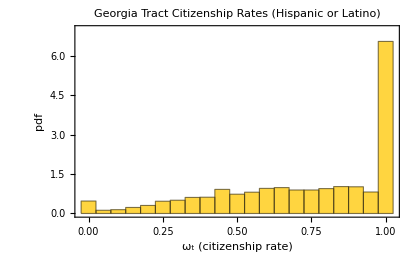

```mathematica
Show[{
Histogram[
Quiet[N@cvap/vap],{0-0.05/2,1+0.05/2,0.05},"PDF",
Frame->True,
FrameLabel->{"ω_t (citizenship rate)","pdf"},
PlotLabel->"Georgia Tract Citizenship Rates (Hispanic or Latino)"
],
Plot[{
Style[Evaluate[PDF[fitBetaBinomialPrior[vap,cvap],x]],Transparent],
Style[Evaluate[PDF[fitBetaBinomialPrior@@Transpose@Discard[Transpose@{vap,cvap},Apply[#1===#2&]],x]],Transparent]
},{x,0,1},PlotRange->{{0,1},{0,7}}]
}]
```

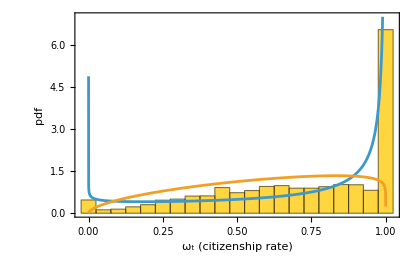

```mathematica
Show[{
Histogram[
Quiet[N@cvap/vap],{0-0.05/2,1+0.05/2,0.05},"PDF",
Frame->True,
FrameLabel->{"ω_t (citizenship rate)","pdf"}
],
Plot[{
Evaluate[PDF[fitBetaBinomialPrior[vap,cvap],x]],
Evaluate[PDF[fitBetaBinomialPrior@@Transpose@Discard[Transpose@{vap,cvap},Apply[#1===#2&]],x]]
},{x,0,1},PlotRange->{{0,1},{0,7}}]
}]
```

```mathematica
Show[{
Histogram[
N@cvap/vap,{0.05},"PDF",
Frame->True,
FrameLabel->{"ω_t (citizenship rate)","pdf"},
Epilog->{Dashed,StandardRed,InfiniteLine[{Mean@dist,0},{0,1}]}
],
Plot[Evaluate[PDF[dist,x]],{x,0,1},PlotRange->{{0,1},{0,7}}],
Plot[Evaluate[PDF[dist,x]],{x,0,1},PlotRange->{{0,1},{0,7}}]
}]
```

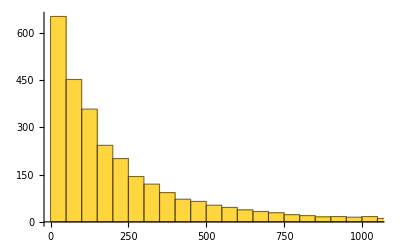

```mathematica
Histogram@vap
```

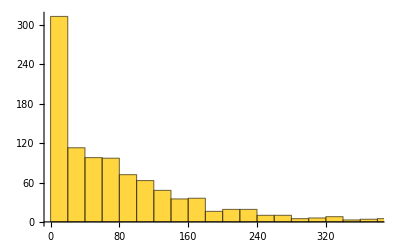

```mathematica
Histogram@vap[[Select[Transpose[{vap,cvap}],Apply[#1===#2&]->"Index"]]]
```

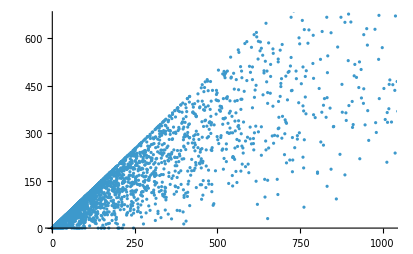

```mathematica
ListPlot@Transpose@{vap,cvap}
```

### Mixture model

```mathematica
logSumExp[x0_]:=With[{x=DeleteCases[x0,-Infinity]},{m=Max[x]},If[Length[x]==1,First[x],m+Log[Total@Exp[x-m]]]]
```

```mathematica
fitZeroOneInflatedBetaBinomialPrior[super_,sub_]:=
Module[{ll,α,β,p0,p1,p2},
ll=Total@N@MapThread[
logSumExp[{
If[#2==0,Log[p0/(p0+p1+p2)],-Infinity],
If[#1==#2,Log[p1/(p0+p1+p2)],-Infinity],
Log[p2/(p0+p1+p2)]+betaBinomialLogLikelihood[BetaBinomialDistribution[α,β,#1],#2]
}]&,
{super,sub}
];
{α,β,p0,p1,p2}=NArgMax[{
ll,
0<α,
0<β,
0<=p0<=1,
0<=p1<=1,
0<=p2<=1
},
{α,β,p0,p1,p2}
];
<|
"BetaDistribution"->BetaDistribution[α,β],
"ZeroSpike"->p0/(p0+p1+p2),
"OneSpike"->p1/(p0+p1+p2),
"PDF"->Function[x,Evaluate@PiecewiseExpand@Piecewise[{
{p0/(p0+p1+p2)*DiracDelta[x]+p2/(p0+p1+p2)*PDF[BetaDistribution[α,β],x],x==0},
{p1/(p0+p1+p2)*DiracDelta[x-1]+p2/(p0+p1+p2)*PDF[BetaDistribution[α,β],x],x==1},
{p2/(p0+p1+p2)*PDF[BetaDistribution[α,β],x],True}
}]]
|>
]
```

```mathematica
(*fitZeroOneInflatedBetaBinomialPrior[super_,sub_]:=Module[{n,x,isZero,isFull,logBinom,ll,la,lb,u1,u2,z},n=N[super];x=N[sub];
isZero=1-Unitize[sub];(*1 where sub==0*)isFull=1-Unitize[sub-super];(*1 where sub==super*)logBinom=LogGamma[n+1]-LogGamma[x+1]-LogGamma[n-x+1];
ll[la_?NumericQ,lb_?NumericQ,u1_?NumericQ,u2_?NumericQ]:=Module[{a=Exp[la],b=Exp[lb],zz=1+Exp[u1]+Exp[u2],q0,q1,q2,bb},q0=1/zz;q1=Exp[u1]/zz;q2=Exp[u2]/zz;
bb=logBinom-LogGamma[a]+LogGamma[x+a]-LogGamma[b]+LogGamma[n-x+b]+LogGamma[a+b]-LogGamma[n+a+b];
Total[Log[isZero q0+isFull q1+q2 Exp[bb]]]];
{la,lb,u1,u2}=NArgMax[ll[la,lb,u1,u2],{la,lb,u1,u2}];
z=1+Exp[u1]+Exp[u2];
<|"alpha"->Exp[la],"beta"->Exp[lb],"p0"->1/z,"p1"->Exp[u1]/z,"p2"->Exp[u2]/z|>]*)
```

```mathematica
(*fitZeroOneInflatedBetaBinomialPrior[super_,sub_]:=
Module[{ll,α,β,p0,p1,x},
ll[α_?NumericQ,β_?NumericQ,p0_?NumericQ,p1_?NumericQ]:=
If[!(0<α&&0<β&&0<=p0&&0<=p1&&p0+p1<=1),
-$MaxMachineNumber,
Total@N@MapThread[
logSumExp[{
If[#2==0,Log[p0],-Infinity],
If[#1==#2,Log[p1],-Infinity],
Log[1-p0-p1]+betaBinomialLogLikelihood[BetaBinomialDistribution[α,β,#1],#2]
}]&,
{super,sub}
]
];
{α,β,p0,p1}=NArgMax[{
ll[α,β,p0,p1],
0<α,
0<β,
0<=p0<=1,
0<=p1<=1,
p0+p1<=1
},
{α,β,p0,p1}
];
<|
"BetaDistribution"->BetaDistribution[α,β],
"ZeroSpike"->p0,
"OneSpike"->p1,
"PDF"->Function[x,Evaluate@Piecewise[{
{p0+(1-p0-p1)*PDF[BetaDistribution[α,β],x],x==0},
{p1+(1-p0-p1)*PDF[BetaDistribution[α,β],x],x==1},
{(1-p0-p1)*PDF[BetaDistribution[α,β],x],True}
}]]
|>
]*)
```

```mathematica
fit=fitZeroOneInflatedBetaBinomialPrior[vap,cvap]//EchoTiming
```

5.19247

<|BetaDistribution→BetaDistribution[1.93392,1.15793],ZeroSpike→0.0184834,OneSpike→0.287179,PDF→Function[x$,Piecewise[{{0., x$>1||x$<0}, {1.67086 (1-x$)^0.157931 x$^0.933916, 0<x$<1}, {0.287179 DiracDelta[-1+x$], x$==1}, {0.0184834 DiracDelta[x$], True}}]]|>

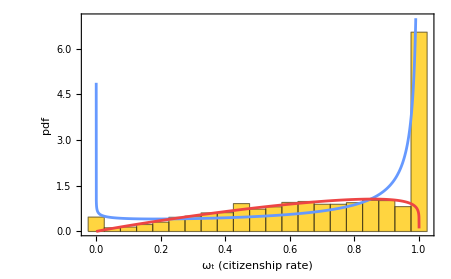

```mathematica
Show[{
Histogram[
Quiet[N@cvap/vap],{0-0.05/2,1+0.05/2,0.05},"PDF",
Frame->True,
FrameLabel->{"ω_t (citizenship rate)","pdf"}
],
Plot[Evaluate@{
PDF[fitBetaBinomialPrior[vap,cvap],x],
fit["PDF"][x]
},
{x,0,1},
PlotRange->{{0,1},{0,7}},
PlotStyle->{StandardBlue,StandardRed}
]
}]
```

### Old version

```mathematica
Values@acsTracts[[All,Key@{"HispanicOrLatino","CVAP"}]]===cvap
```

True

```mathematica
Values@acsTracts[[All,Key@{"HispanicOrLatino","VAP"}]]===vap
```

True

```mathematica
Min@blockCVAPACS[[All,"HispanicOrLatino",1]]
```

0.953196

```mathematica
Min@blockCVAPACS[[All,"HispanicOrLatino",2]]
```

0.310371

### Automatic casting

```mathematica
Import["https://api.census.gov/data/2022/acs/acs5/variables.json","RawJSON"]
```